```mathematica
Plot[2x+1,{x,-1,2},PlotRange->{-0.2,4},AxesLabel->{x,y},Ticks->{{-1,1,2},{1,3}}]
```

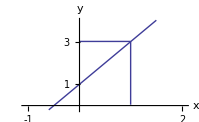

```mathematica
Plot[0.3y+12,{y,87,93},PlotRange->{37,40},AxesLabel->{y,c},{AxesOrigin->Automatic},Ticks->{{90},{39}}]
```

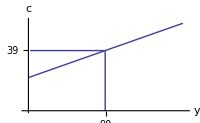

```mathematica
Plot[80-2p,{p,0,35},PlotRange->{0,85},AxesLabel->{p,Q},Ticks->{{10,20},{40,60,80}}]
```

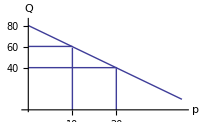

```mathematica
p1=Plot3D[k^0.5 l^0.5,{k,0,5},{l,0,5},Ticks->{{1,4},{1,4}},AxesLabel->{K,L,Q},Mesh->None,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[0.4]],ExclusionsStyle->{None,Blue}]
```

-Graphics3D-

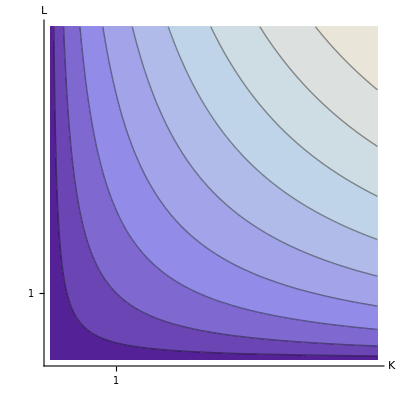

```mathematica
p2=ContourPlot[k^0.5 l^0.5,{k,0,5},{l,0,5},Ticks->{{1},{1}},AxesLabel->{K,L},Axes->True,Frame->False]
```

```mathematica
w1=Plot[{x+1},{x,0,2},Ticks->{{},{}},AxesLabel->{x,y},PlotRange->{0,4}]
```

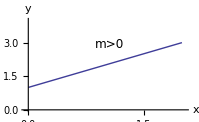

```mathematica
Plot[{-x+3},{x,0,2},Ticks->{{},{}},AxesLabel->{x,y},PlotRange->{0,4}]
```

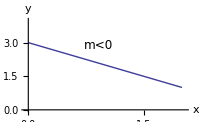

```mathematica
Plot[{1},{x,0,2},Ticks->{{},{}},AxesLabel->{x,y},PlotRange->{0,2}]
```

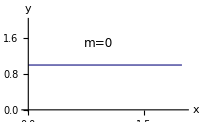

```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
Plot[ⅇ^x,{x,-1.2,2.5},Ticks->{{},{}},AxesLabel->{x,y}]
```

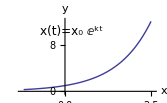

```mathematica
Plot[ⅇ^-x,{x,-1,3},Ticks->{{},{}},AxesLabel->{x,y}]
```

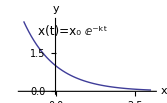

```mathematica
Plot[Log[x],{x,0,9},AxesLabel->{x,y},Ticks->{{},{}}]
```

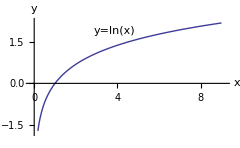

```mathematica
Plot[(x^2-1)/(x-1),{x,-0.2,2},PlotRange->{-0.4,3},AxesLabel->{x,f[x]},Ticks->{{1},{2}}]
```

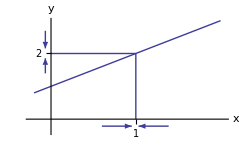

```mathematica
Plot[(x^2-3x-10)/(x-5),{x,-1,9},PlotRange->{0,11},AxesLabel->{x,f[x]},Ticks->{{5},{7}}]
```

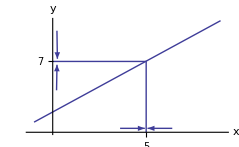

```mathematica
Plot[x^2/(1+x+2 x^2),{x,-30,30},PlotRange->{-0.1,1},AxesLabel->{Infinity,f[x]},Ticks->{{},{}}]
```

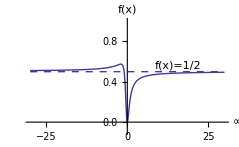

```mathematica
Plot[5+1/x,{x,-0.1,20},PlotRange->{-0.1,12},AxesLabel->{Infinity,f[x]},Ticks->{{},{5}}]
```

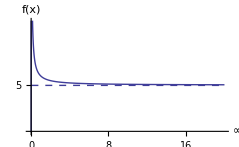

```mathematica
Plot[(3 x^2+x-1)/(x^2+1),{x,-3,14},PlotRange->{-2,5},AxesLabel->{Infinity,y},Ticks->{{},{3}}]
```

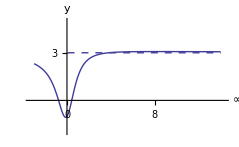

```mathematica
Plot[2+ⅇ^(-2x),{x,-0.5,6},PlotRange->{-0.5,5},AxesLabel->{Infinity,y},Ticks->{{},{2,3}}]
```

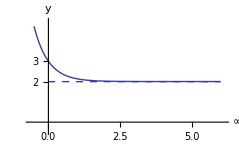

```mathematica
Plot[1+20 ⅇ^(-0.01x)-16 ⅇ^(-0.02x),{x,-0.9,1000},PlotRange->{-0.1,8},AxesLabel->{Infinity,y},Ticks->{{},{1,5,7}}]
```

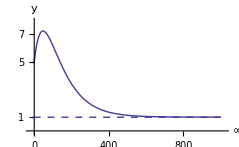

```mathematica
f1[x_]=x^3+x+2
```

2+x+x^3

```mathematica
f1[-2]
```

-8

```mathematica
f1[1]
```

4

```mathematica
Plot[x^3+x+2,{x,-2.4,1.5},PlotRange->{-9,5},AxesLabel->{x,f[x]},Ticks->{{-2,-1,1},{-8,4}}]
```

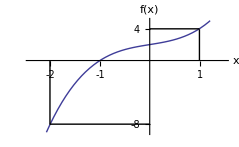

```mathematica
Plot[2 x^3+3 x^2-12x-7,{x,-3,2},PlotRange->{-16,15},AxesLabel->{x,f[x]},Ticks->{{-2,1},{-14,13}}]
```

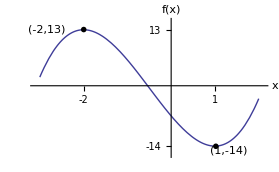

```mathematica
Plot[1+20 ⅇ^(-0.1t)-16 ⅇ^(-0.2t),{t,-0.1,100},PlotRange->{0,8},AxesLabel->{Infinity,p[t]},Ticks->{{},{5,7,1}}]
```

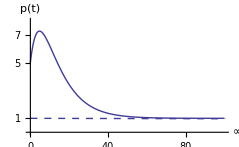

```mathematica
p[t_]=1+20 ⅇ^(-0.1t)-16 ⅇ^(-0.2t)
```

1-16 ⅇ^(-0.2 t)+20 ⅇ^(-0.1 t)

```mathematica
p[22]
```

3.01963

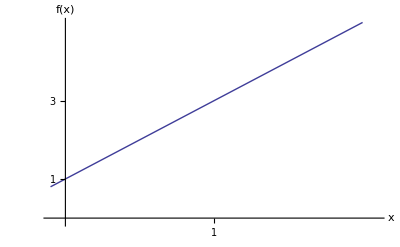

```mathematica
Plot[2x+1,{x,-0.1,2.1},PlotRange->{-0.1,5},AxesLabel->{x,f[x]},Ticks->{{1},{1,3}}]
```

```mathematica
Plot[2x+1,{x,-1,2},PlotRange->{-1,5},AxesLabel->{x,f[x]},Ticks->{{1},{1,2,3}}]
```

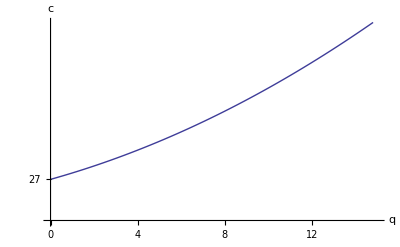

```mathematica
Plot[1/5 q^2+4q+27,{q,0,15},PlotRange->{-1,130},AxesLabel->{q,c},Ticks->{{},{27}}]
```

```mathematica
N[2/5*8+4]
```

7.2

```mathematica
2/5*8+4
```

36/5

```mathematica
c[q_]=1/5 q^2+4q+27
```

27+4 q+q^2/5

```mathematica
N[c[9]-c[8]]
```

7.4

```mathematica
75-6(8)
```

27

```mathematica
r[q_]=75q-3 q^2
```

75 q-3 q^2

```mathematica
r[9]-r[8]
```

24

```mathematica
Plot[{75q-q^2,100q-q^2,25q},{q,0,100},PlotRange->{0,2600},AxesLabel->{q,{π,R,c}},Ticks->{{37.5},{1406.25}}]
```

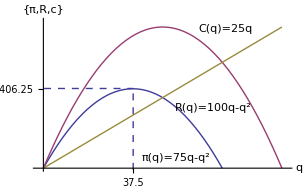

```mathematica
Plot[{25,100-q,100-2q},{q,0,75},PlotRange->{0,105},AxesLabel->{q,{p,R',C'}},Ticks->{{37.5},{25,62.5,100}}]
```

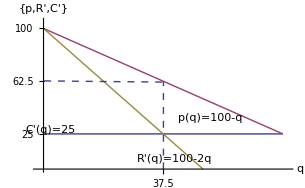

```mathematica
ContourPlot[{50 l^(2/3)k^(1/3)==8254.818122236567,300k+100l==45000},{l,0,500},{k,0,160},Ticks->{{300},{50}},AxesLabel->{L,K},Axes->True,Frame->False]
```

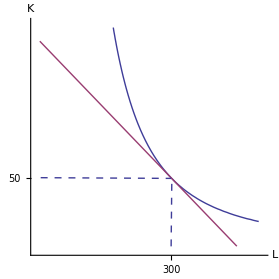

```mathematica
N[10(18)^(3/5)(8)^(2/5)]
```

130.137

```mathematica
ContourPlot[{10 x^(3/5)y^(2/5)==130.13661254372388,20x+30y==600},{x,0,35},{y,0,25},Ticks->{{18},{8}},AxesLabel->{x,y},Axes->True,Frame->False]
```

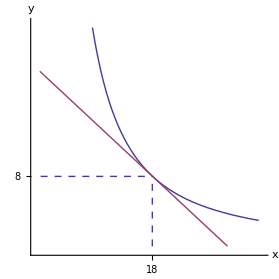

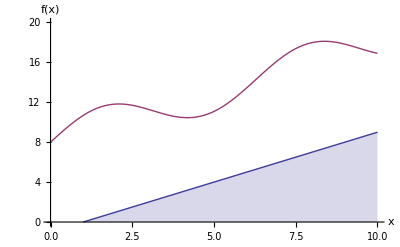

```mathematica
Plot[{x-1,2Sin[x]+x+8},{x,0,10},PlotRange->{0,20},AxesLabel->{x,f[x]},Ticks->{{},{}},Filling->{1->Axis}]
```

```mathematica
Plot[-0.2 t^3+3 t^2+100,{t,0,9},PlotRange->{90,200},AxesLabel->{t,I},Ticks->{{5},{}}]
```

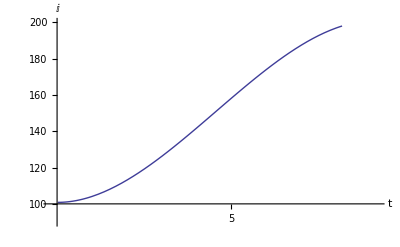

```mathematica
ContourPlot[{4 l^(1/2)k^(3/4)==32,4 l^(1/2)k^(3/4)==54,4 l^(1/2)k^(3/4)==76},{l,0,6},{k,0,60},Ticks->{{{0,0}},{{0,0}}},AxesLabel->{L,K},Axes->True,Frame->False]
```

```mathematica
N[16^(3/4)]
```

8.

```mathematica
Plot[10+0.5y,{y,-0.1,20},PlotRange->{-0.1,20},AxesLabel->{y,c},Ticks->{{},{10}}]
```

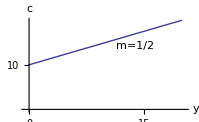

```mathematica
Plot[15-2r,{r,0,5},PlotRange->{-0.1,18},AxesLabel->{r,I},Ticks->{{},{15}}]
```

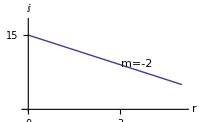

```mathematica
Plot[50-4r,{r,0,8},PlotRange->{-0.1,60},AxesLabel->{r,Y},Ticks->{{},{50}}]
```